```mathematica
A={0.669,1.265,2.075,3.325, 4.814, 6.772, 8.808, 12.803, 14.103, 17.176}
```

{0.669,1.265,2.075,3.325,4.814,6.772,8.808,12.803,14.103,17.176}

```mathematica
B=Table[10000+(i+1)*10000,{i,0,9}]
```

{20000,30000,40000,50000,60000,70000,80000,90000,100000,110000}

```mathematica
CC=Transpose@{B,A}
```

{{20000,0.669},{30000,1.265},{40000,2.075},{50000,3.325},{60000,4.814},{70000,6.772},{80000,8.808},{90000,12.803},{100000,14.103},{110000,17.176}}

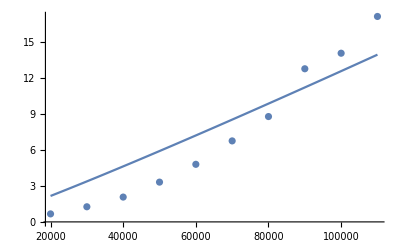

```mathematica
Show[ListPlot[Transpose@{B,A}],Plot[0.000010949414499786434 n Log[n],{n,20000,110000}]]
```

```mathematica
NonlinearModelFit[CC,a  n Log[2,n],{a},n]
```

FittedModel[0.0000109494 n Log[n]]

```mathematica
A1={0.226, 0.63, 1.149, 2.026, 3.196, 4.643, 6.427, 8.64, 10.903, 13.621}
```

{0.226,0.63,1.149,2.026,3.196,4.643,6.427,8.64,10.903,13.621}

```mathematica
B1=Table[10000+(i)*10000,{i,0,9}]
```

{10000,20000,30000,40000,50000,60000,70000,80000,90000,100000}

```mathematica
CC1=Transpose@{B1,A1}
```

{{10000,0.226},{20000,0.63},{30000,1.149},{40000,2.026},{50000,3.196},{60000,4.643},{70000,6.427},{80000,8.64},{90000,10.903},{100000,13.621}}

```mathematica
NonlinearModelFit[CC1,a  n Log[2,n],{a},n]
```

FittedModel[9.44114×10^-6 n Log[n]]

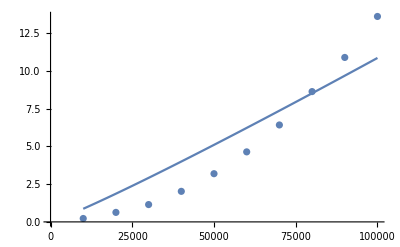

```mathematica
Show[ListPlot[CC1],Plot[9.441135585593725*^-6 n Log[n],{n,10000,100000}]]
```

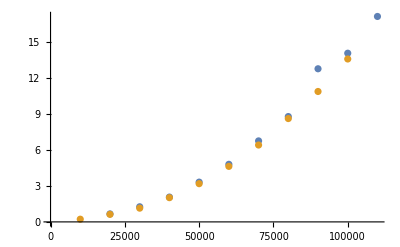

```mathematica
Show[ListPlot[{CC,CC1}]]
```

```mathematica
Total[A1]
```

```mathematica
51.461*50
```

```mathematica
2573.0499999999997/60
```

42.8842

```mathematica
A={{0.159,0.642,1.14,2.156,3.548,4.752,7.146,9.972,12.126,15.581},{0.159,0.76,1.549,2.346,3.637,5.333,7.322,9.306,12.373,15.138},{0.157,0.554,1.27,2.31,3.633,5.148,7.293,9.753,12.505,15.418},{0.166,0.63,1.346,2.382,3.855,5.428,7.445,9.551,12.364,15.442},{0.154,0.578,1.274,2.252,3.554,5.259,7.122,9.499,12.106,14.285},{0.167,0.581,1.278,2.257,3.719,5.602,7.146,8.838,11.285,14.579},{0.149,0.578,1.217,2.2,3.809,5.206,7.151,9.645,12.549,13.895},{0.166,0.554,1.283,2.241,3.554,5.032,6.947,9.18,11.315,14.169},{0.147,0.522,1.277,2.26,3.559,4.969,7.002,9.067,10.756,13.287},{0.126,0.512,1.139,2.02,3.212,4.677,6.415,8.513,10.713,13.561},{0.13,0.494,1.122,2.047,3.935,5.546,7.659,10.093,13.017,14.968},{0.154,0.577,1.428,2.439,3.757,5.33,7.58,9.873,12.684,15.13},{0.156,0.57,1.351,2.436,3.839,5.313,7.357,9.903,12.074,15.006},{0.186,0.627,1.367,2.344,3.844,5.514,7.709,9.417,12.745,15.864},{0.152,0.55,1.262,2.238,3.569,5.021,6.747,9.306,11.803,14.306},{0.144,0.629,1.317,2.293,3.564,5.429,7.658,9.536,12.346,15.209},{0.182,0.622,1.315,2.311,3.887,5.298,7.328,9.573,12.81,15.28},{0.164,0.585,1.352,2.4,3.761,5.276,7.515,9.512,12.394,15.385},{0.153,0.56,1.253,2.328,3.818,5.091,7.077,9.354,12.779,15.291},{0.167,0.564,1.357,2.31,3.682,5.429,7.052,9.515,11.907,15.272},{0.158,0.594,1.273,2.312,3.924,5.502,7.312,9.396,12.546,13.798},{0.148,0.576,1.37,2.243,3.309,4.987,6.767,8.546,10.751,13.41},{0.129,0.475,1.136,2.026,3.211,4.759,6.421,8.423,10.873,13.498},{0.135,0.501,1.136,2.017,3.186,4.631,6.384,8.426,10.906,13.735},{0.125,0.485,1.164,2.053,3.314,4.819,6.917,8.616,11.137,13.436},{0.123,0.518,1.144,2.017,3.216,5.02,6.583,8.288,10.841,13.334},{0.127,0.489,1.094,2.022,3.218,4.634,6.503,8.64,10.999,13.366},{0.129,0.497,1.137,1.993,3.191,4.687,6.495,8.409,10.744,13.486},{0.157,0.494,1.136,2.087,3.518,4.914,6.6,9.339,12.086,13.616},{0.112,0.551,1.201,2.059,3.262,4.903,6.562,8.318,10.605,13.697},{0.147,0.552,1.2,2.223,3.401,4.764,6.32,8.512,10.91,13.235},{0.091,0.51,1.139,1.992,3.187,4.711,6.449,8.424,10.754,13.585},{0.122,0.476,1.102,2.028,3.187,4.743,6.323,8.566,10.766,13.306},{0.125,0.469,1.134,2.066,3.294,4.706,6.384,8.36,10.624,13.327},{0.129,0.479,1.137,2.081,3.349,4.73,6.356,8.541,10.882,13.297},{0.125,0.498,1.131,2.142,3.3,4.781,6.442,8.659,10.749,13.822},{0.135,0.595,1.169,2.032,3.223,4.602,6.483,8.53,11.013,13.554},{0.132,0.509,1.124,2.028,3.286,4.713,6.877,9.348,12.116,14.163},{0.146,0.535,1.174,2.184,3.383,5.087,7.065,8.969,11.587,13.55},{0.134,0.514,1.194,2.007,3.419,4.658,6.736,8.907,12.14,14.306},{0.134,0.491,1.245,2.143,3.338,4.889,6.687,9.677,11.845,13.453},{0.195,0.588,1.615,2.348,3.377,4.878,7.162,8.883,12.065,15.393},{0.158,0.566,1.231,2.236,3.653,5.199,6.946,8.704,12.362,14.83},{0.161,0.579,1.35,2.252,3.765,5.4,7.737,9.299,11.813,15.97},{0.157,0.61,1.38,2.636,3.869,5.315,7.429,9.908,11.567,13.245},{0.155,0.592,1.291,2.139,3.283,4.642,6.506,8.507,10.97,13.812},{0.126,0.501,1.126,2.019,3.178,4.671,6.411,8.426,10.752,13.423},{0.123,0.498,1.125,2.031,3.166,4.64,6.402,8.481,10.722,13.472},{0.151,0.505,1.122,2.094,3.878,5.386,7.547,10.105,12.684,14.479},{0.155,0.576,1.34,2.354,3.775,5.312,7.43,9.219,11.819,15.178} };
```

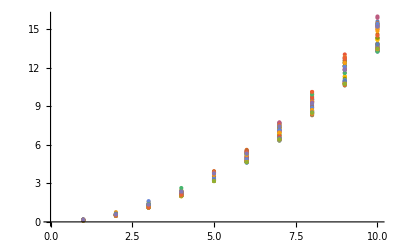

```mathematica
ListPlot[A]
```

```mathematica
CT=Table[Sum[A[[i,j]]/50,{i,1,Length[A]}],{j,1,Length[A[[1]]]}]
```

{0.14564,0.55024,1.24034,2.18868,3.50792,5.02672,6.93814,9.07664,11.6456,14.2368}

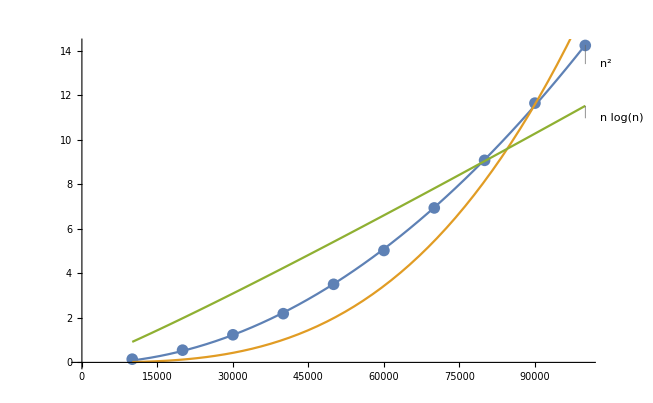

```mathematica
Show[{ListPlot[Transpose@{B1,CT}],Plot[ {-0.05569512087912153+1.4315244469815898*^-9 n^2,1.589960766374933*^-14 n^3,0.000010009637386542001 n Log[n]},{n,10000,100000},PlotLabels->{n^2,n^3,n Log[ n]}]}]
```

```mathematica
NonlinearModelFit[Transpose@{B1,CT},a n Log10[n],{a,b},n]
```

FittedModel[0.0000100096 n Log[n]]

```mathematica
Transpose@{B,CT}
```

{{20000,0.14564},{30000,0.55024},{40000,1.24034},{50000,2.18868},{60000,3.50792},{70000,5.02672},{80000,6.93814},{90000,9.07664},{100000,11.6456},{110000,14.2368}}